Prelim work on how to decompose an unitary matrix into the CKM parameter forms.

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Peggy/Projects/physics_5d_flavourful_axion_neutrino/mathematica

```mathematica
<<"WarpFlavourAxion`"
```

### Functions

#### CKM matrix

```mathematica
Ckm[t12_,t13_,t23_,delta_]:=({{1, 0, 0}, {0, Cos[t23], Sin[t23]}, {0, -Sin[t23], Cos[t23]}}).({{Cos[t13], 0, Sin[t13]Exp[-I delta]}, {0, 1, 0}, {-Sin[t13]Exp[I delta], 0, Cos[t13]}}).({{Cos[t12], Sin[t12], 0}, {-Sin[t12], Cos[t12], 0}, {0, 0, 1}})
```

Check the real value

```mathematica
Map[Abs,Ckm[13.04 Degree, 0.201 Degree, 2.38 Degree, 1.20],{-1}]//MatrixForm
```

(0.974207 | 0.22563 | 0.0035081
0.225488 | 0.973361 | 0.0415266
0.00873301 | 0.0407493 | 0.999131)

The actual value is

(0.97427±0.00015 | 0.22534±0.00065 | 0.00351±0.00015
0.22520±0.00065 | 0.97344±0.00016 | 0.0412±0.0011
0.00867±0.00031 | 0.0404±0.0011 | 0.999146±0.000046)

```mathematica
GetCKMthetas[unitaryMatrix_]:=Module[{abss,args,c12,c13,c23},
(* unitaryMatrix must be 3 by 3 matrix *)
abss=Map[Abs,unitaryMatrix,{-1}];
args=Map[Arg,unitaryMatrix,{-1}];
c13 = Sqrt[1-abss[[1, 3]]^2];
c12 = abss[[1, 1]]/c13;
c23 = abss[[3, 3]]/c13;
(* output theta angles *)
{ArcCos[c12],ArcCos[c13],ArcCos[c23]}
]
```

```mathematica
GetCKMParameters[unitaryMatrix_]:=Module[{abss,args,c12,c13,c23,s12,s13,s23,delta,u1},
(* unitaryMatrix must be 3 by 3 matrix *)
abss=Map[Abs,unitaryMatrix,{-1}];
args=Map[Arg,unitaryMatrix,{-1}];

(* CKM parameters *)
s13=abss[[1, 3]];c13 = Sqrt[1-s13^2];
c12 = abss[[1, 1]]/c13;s12=Sqrt[1-c12^2];
c23 = abss[[3, 3]]/c13;s23=Sqrt[1-c23^2];

(* solving for rotation parameters *)
u1=1/2 Arg[-
Exp[-I/3(4 args[[1,1]]+args[[1,2]]+2 args[[2, 3]]+2 args[[3, 3]])] (Exp[I( args[[2, 1]]+ args[[3, 3]])]c23 abss[[2,1]] -Exp[I(args[[2, 3]]+args[[3, 1]])]s23 abss[[3,1]])
];
(* solving for the CP phase *)
delta=Mod[2Pi-1/3(6u1+args[[1,1]]+args[[1,2]]+3args[[1,3]]-args[[2 ,3]]-args[[3,3]]),2Pi];

(* output {CKM parameter, phi_u, phi_d} *)
{
{ArcCos[c12],ArcCos[c13],ArcCos[c23],delta},
{u1,
-u1+1/3 (-args[[1,1]]-args[[1,2]]-2 args[[2,3]]+args[[3,3]]),
-u1+1/3 (-args[[1,1]]-args[[1,2]]+args[[2,3]]-2 args[[3,3]])},
{u1+args[[1,1]],
u1+args[[1,2]],
-u1+1/3 (-args[[1,1]]-args[[1,2]]+args[[2,3]]+args[[3,3]])}
}
]
```

### Workspace

```mathematica
m = RandomUnitaryMatrix[3, 0.1, 4];
m//MatrixForm
```

(-0.0723111-0.653587 ⅈ | -0.0374169+0.18338 ⅈ | 0.466396+0.561286 ⅈ
-0.457278-0.324634 ⅈ | -0.369155+0.477576 ⅈ | -0.541299-0.167783 ⅈ
-0.417584-0.280586 ⅈ | 0.246198-0.73485 ⅈ | -0.345831+0.163338 ⅈ)

```mathematica
m= {
{(-0.6172793291062022-0.12243613860981267I),(0.5084885671803796-0.489200419247175I), (0.2727797775870358-0.17801444215376286I)},
{(-0.04928590865099306-0.5355437544935865I), (-0.29260820623132106+0.10273110586065624I), (-0.12706133045873297-0.7735928916866746I)},
{(-0.09426843489504314-0.5530396642505069I), (-0.4439850292872076-0.4569752489564456I), (-0.11713696213209661+0.5153546736574932I)}
}
```

{{-0.617279-0.122436 ⅈ,0.508489-0.4892 ⅈ,0.27278-0.178014 ⅈ},{-0.0492859-0.535544 ⅈ,-0.292608+0.102731 ⅈ,-0.127061-0.773593 ⅈ},{-0.0942684-0.55304 ⅈ,-0.443985-0.456975 ⅈ,-0.117137+0.515355 ⅈ}}

```mathematica
{ckms,phiu, phid} =GetCKMParameters[m]
```

{{0.842493,0.33178,0.977636,0.985306},{0.425205,2.5659,-0.961979},{-2.52058,-0.340863,0.832314}}

These two matrices should be exactly the same

```mathematica
Ckm@@ckms  //Chop// MatrixForm
DiagonalMatrix[Exp[I phiu]].m.DiagonalMatrix[Exp[-I phid]]// Chop// MatrixForm
```

(0.657575 | 0.187158 | -0.194317-0.703426 ⅈ
0.00177869-0.560791 ⅈ | 0.582133-0.159612 ⅈ | 0.566706
0.331457-0.378472 ⅈ | -0.767472-0.10772 ⅈ | 0.382463)

(0.657575 | 0.187158 | -0.194317-0.703426 ⅈ
0.00177869-0.560791 ⅈ | 0.582133-0.159612 ⅈ | 0.566706
0.331457-0.378472 ⅈ | -0.767472-0.10772 ⅈ | 0.382463)

These two matrices should be exactly the same

```mathematica
Map[Abs,Ckm@@ckms ,{-1}] //Chop// MatrixForm
Map[Abs,DiagonalMatrix[Exp[I phiu]].m.DiagonalMatrix[Exp[-I phid]],{-1}]// Chop// MatrixForm
```

(0.885434 | 0.453224 | 0.102931
0.0247854 | 0.175878 | 0.9841
0.464104 | 0.873873 | 0.144751)

(0.885434 | 0.453224 | 0.102931
0.0247854 | 0.175878 | 0.9841
0.464104 | 0.873873 | 0.144751)

```mathematica
(* 
{u1,m1,v1}=SingularValueDecomposition[y1tilde];
{u2,m2,v2}=SingularValueDecomposition[y2tilde];
mat = y1.ConjugateTranspose[v2]; ckmsTemp = GetCKMParameters[mat][[1]];
Abs[((ckmsTemp[[1]]-$CkmTheta12)/($CkmTheta12Sigma))^2+((ckmsTemp[[2]]-$CkmTheta13)/($CkmTheta13Sigma))^2+((ckmsTemp[[3]]-$CkmTheta23)/($CkmTheta23Sigma))^2+((ckmsTemp[[4]]-$CkmDelta)/($CkmDeltaSigma))^2]
*)
```

```mathematica
SquaredError[y1_,y2_,cL1_,cL2_,cL3_,mcR11_,mcR12_,mcR13_,mcR21_,mcR22_,mcR23_,zuv_:1.01,zir_:10]:=Module[{y1tilde,y2tilde,u1,m1,v1,u2,m2,v2,mat,ckmsTemp},
(*  *)
y1tilde=DiagonalMatrix[{FermionProfile[cL1,zuv,zir,zuv] ,FermionProfile[cL2,zuv,zir,zuv] ,FermionProfile[cL3,zuv,zir,zuv]}].y1.DiagonalMatrix[{FermionProfile[mcR11,zuv,zir,zuv] ,FermionProfile[mcR12,zuv,zir,zuv] ,FermionProfile[mcR13,zuv,zir,zuv]}];
y2tilde=DiagonalMatrix[{FermionProfile[cL1,zuv,zir,zuv] ,FermionProfile[cL2,zuv,zir,zuv] ,FermionProfile[cL3,zuv,zir,zuv]}].y2.DiagonalMatrix[{FermionProfile[mcR21,zuv,zir,zuv] ,FermionProfile[mcR22,zuv,zir,zuv] ,FermionProfile[mcR23,zuv,zir,zuv]}];
{u1,m1,v1}=SingularValueDecomposition[y1tilde];
{u2,m2,v2}=SingularValueDecomposition[y2tilde];
mat = y1.ConjugateTranspose[v2]; ckmsTemp = GetCKMParameters[mat][[1]];
Abs[((ckmsTemp[[1]]-$CkmTheta12)/($CkmTheta12Sigma))^2+((ckmsTemp[[2]]-$CkmTheta13)/($CkmTheta13Sigma))^2+((ckmsTemp[[3]]-$CkmTheta23)/($CkmTheta23Sigma))^2+((ckmsTemp[[4]]-$CkmDelta)/($CkmDeltaSigma))^2]
]
```

```mathematica
y1temp = RandomMatrix[3];y2temp=RandomMatrix[3];
SquaredError[y1temp, y2temp, 3., 2., 1., 1.3, 1.2, 1.1, 1.3, 1.2, 1.1]
```

3.16147×10^8

```mathematica
NMinimize[SquaredError[y1temp,y2temp,c1,c2,c3,d11,d12,d13,d21,d22,d23],
{c1,c2,c3,d11,d12,d13,d21,d22,d23}
]
```

SingularValueDecomposition::svdnsvc: Cannot compute all the singular vectors.

Set::shape: Lists {u1$91624,m1$91624,v1$91624} and SingularValueDecomposition[{{((0.+0. ⅈ)-(1.73825+1.70286 ⅈ) FermionProfile[c1,1.01,10,1.01]) FermionProfile[d11,1.01,10,1.01],((0.+0. ⅈ)-(1.38009-1.462 ⅈ) FermionProfile[c1,1.01,10,1.01]) FermionProfile[d12,1.01,10,1.01],((0.+0. ⅈ)+(0.76492+1.21391 ⅈ) FermionProfile[c1,1.01,10,1.01]) FermionProfile[d13,1.01,10,1.01]},«1»,{((0.+0. ⅈ)-(0.263547+2.41536 ⅈ) FermionProfile[c3,1.01,10,1.01]) FermionProfile[d11,1.01,10,1.01],«1»,((0.+0. ⅈ)+(0.00815168+0.095465 ⅈ) FermionProfile[c3,1.01,10,1.01]) «14»[«1»]}}] are not the same shape.

SingularValueDecomposition::svdnsvc: Cannot compute all the singular vectors.

Set::shape: Lists {u2$91624,m2$91624,v2$91624} and SingularValueDecomposition[«1»] are not the same shape.

Part::partw: Part 3 of {{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]] does not exist.

Part::partw: Part 3 of ConjugateTranspose[Arg[v2$91624]] does not exist.

Part::partw: Part 3 of {{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::bcons: The following constraints are not valid: {Abs[(1.49127×10^6-2.51454×10^6 ⅈ)+1.92901×10^6 (-0.04054+ArcCos[Times[«2»]])^2+516.529 (-1.196+Mod[Plus[«2»],Times[«2»]])^2],Abs[(-2.2369×10^6-1.65985×10^6 ⅈ)+1.92901×10^6 (-0.04054+ArcCos[Times[«2»]])^2+516.529 (-1.196+Mod[Plus[«2»],Times[«2»]])^2]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinimize[{Abs[(1.34044×10^7-4.71113×10^8 ⅈ)+1.92901×10^6 (-0.04054+ArcCos[(0.-0.451597 ⅈ) ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧])^2+516.529 (-1.196+Mod[2 π+1/3 (8.69708-3 Arg[-ⅇ^(-1/3 ⅈ (-10.7581+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) ((0.-0.451597 ⅈ) ⅇ^(ⅈ (Arg[v2$91624]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) Abs[v2$91624] ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧-ⅇ^(ⅈ (({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,1⟧)) ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,1⟧ √(1+(0.20394+0. ⅈ) (({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧)^2))]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧),2 π])^2],Abs[(1.49127×10^6-2.51454×10^6 ⅈ)+1.92901×10^6 (-0.04054+ArcCos[1.04712 ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧])^2+516.529 (-1.196+Mod[2 π+1/3 (4.72918-3 Arg[-ⅇ^(-1/3 ⅈ (11.1726+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) (1.04712 ⅇ^(ⅈ (Arg[v2$91624]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) Abs[v2$91624] ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧-ⅇ^(ⅈ (({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,1⟧)) ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,1⟧ √(1-1.09647 (({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧)^2))]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧),2 π])^2],Abs[(-2.2369×10^6-1.65985×10^6 ⅈ)+1.92901×10^6 (-0.04054+ArcCos[1.00462 ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧])^2+516.529 (-1.196+Mod[2 π+1/3 (-5.95704-3 Arg[-ⅇ^(-1/3 ⅈ (4.52576+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+2 ({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) (1.00462 ⅇ^(ⅈ (Arg[v2$91624]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧)) Abs[v2$91624] ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧-ⅇ^(ⅈ (({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,1⟧)) ({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,1⟧ √(1-1.00927 (({{2.43336,2.0105,1.43481},{2.58093,2.28525,1.96414},{2.42969,0.296611,0.0958124}}.ConjugateTranspose[Abs[v2$91624]])⟦3,3⟧)^2))]+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦2,3⟧+({{-2.36648,2.32738,1.00852},{-1.29216,1.86306,0.491681},{-1.67948,-2.97321,1.48561}}.ConjugateTranspose[Arg[v2$91624]])⟦3,3⟧),2 π])^2]},{c1,c2,c3,d11,d12,d13,d21,d22,d23}]

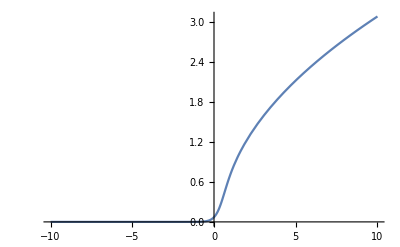

```mathematica
Plot[FermionProfile[c,1.,100.,1.],{c,-10,10}]
```

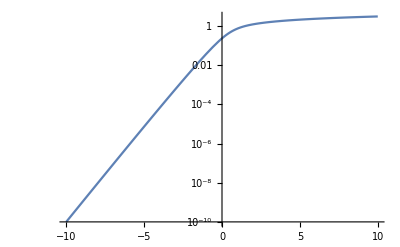

```mathematica
LogPlot[FermionProfile[c,1.,10.,1.],{c,-10,10}]
```

```mathematica
FermionProfile[0., 1.01, 10.]
```

0.240574